```mathematica
(* ClearAll["Global`*"] *)

(* Use these EIS fit values for Rs and Cdl in the low resistance case: *)
-Graphics-;

RsEIS = 1619;
RsEIS = 294;
CdlEIS = 355*10^-9;
squareWaveAmplitude = 0.025 ;(* assume a 25 mV step *)

(* Then, fit Capt, Rct0, Rct1, kD from data. *)
(* Given the Rs, Cdl, Capt, Rct0, Rct1, kD, and known concentrations, generate a predition for current vs frequency with an added resistors, at each of the concentrations tested *)
```

```mathematica
experimentalDataWithNoResistor=Import["C:\\Users\\Bob Lansdorp\\Documents\\Wolfram Mathematica\\aptamerModel\\experimentalData\\2025-11-13\\E3Ir_vs_Freq10Hz_15Hz_20Hz_25Hz_30Hz_40Hz_70Hz_80Hz_100Hz_200Hz_300Hz_400Hz_500Hz_600Hz_.txt","Table"];
(* to do: replace this E3Ir file with Mathematica voltammogram extraction of deltaI and baseline *)

columnHeaders=experimentalDataWithNoResistor[[1]];
data1=experimentalDataWithNoResistor[[2;;]];
frequencies=ToExpression[StringReplace[columnHeaders,"Current_"->""]];

(* use the know concentrations *)
concentrationList=Join[ConstantArray[0.0,4],ConstantArray[1.0*^-5,3],ConstantArray[4.0*^-5,3],ConstantArray[1.0*^-4,3],ConstantArray[3.2*^-4,3],ConstantArray[9.3*^-3,3]];
concentrationList=Take[concentrationList,Length[data1]];

grouped1=GroupBy[Thread[{concentrationList,data1}],First->Last];

(*Identify min and max concentration*)
minConc=Min[Keys[grouped1]];
maxConc=Max[Keys[grouped1]];
```

```mathematica
(*STEP 1:Define giant symbolic model expression*)

(* analyticalBaselineExpression=4 CDL ⅇ^(-3/(CDL fSWV Rsol)) (1-ⅇ^(1/(4 CDL fSWV Rsol))-3 ⅇ^(1/(2 CDL fSWV Rsol))+3 ⅇ^(3/(4 CDL fSWV Rsol))+4 ⅇ^(1/(CDL fSWV Rsol))-4 ⅇ^(5/(4 CDL fSWV Rsol))-4 ⅇ^(3/(2 CDL fSWV Rsol))+4 ⅇ^(7/(4 CDL fSWV Rsol))+4 ⅇ^(2/(CDL fSWV Rsol))-4 ⅇ^(9/(4 CDL fSWV Rsol))-4 ⅇ^(5/(2 CDL fSWV Rsol))+4 ⅇ^(11/(4 CDL fSWV Rsol))) fSWV V0; |*)
analyticalBaselineExpression=4 CDL ⅇ^(-2/(CDL fSWV Rsol)) (-1+ⅇ^(1/(4 CDL fSWV Rsol))) (-1+3 ⅇ^(1/(2 CDL fSWV Rsol))-4 ⅇ^(1/(CDL fSWV Rsol))+4 ⅇ^(3/(2 CDL fSWV Rsol))) fSWV V0;

analyticalBaselineExpression=analyticalBaselineExpression/.{V0->squareWaveAmplitude};


analyticalCHICurrentExpression=-4 CDL ⅇ^(-2/(CDL fSWV Rsol)) (-1+ⅇ^(1/(4 CDL fSWV Rsol))) (-1+3 ⅇ^(1/(2 CDL fSWV Rsol))-4 ⅇ^(1/(CDL fSWV Rsol))+4 ⅇ^(3/(2 CDL fSWV Rsol))) fSWV V0+(2 ⅇ^(-(CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(Capt CDL fSWV Rct Rsol)) fSWV (CDL^2 (-1+ⅇ^((2 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(Capt CDL fSWV Rct Rsol))+ⅇ^((CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(8 Capt CDL fSWV Rct Rsol))+3 ⅇ^((CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(4 Capt CDL fSWV Rct Rsol))-3 ⅇ^((3 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)))/(8 Capt CDL fSWV Rct Rsol))-4 ⅇ^((CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(2 Capt CDL fSWV Rct Rsol))+4 ⅇ^((5 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)))/(8 Capt CDL fSWV Rct Rsol))+4 ⅇ^((3 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)))/(4 Capt CDL fSWV Rct Rsol))-4 ⅇ^((7 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)))/(8 Capt CDL fSWV Rct Rsol))+4 ⅇ^((CDL Rsol+Capt (Rct+Rsol)+3 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(2 Capt CDL fSWV Rct Rsol))-4 ⅇ^((3 CDL Rsol+3 Capt (Rct+Rsol)+5 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(4 Capt CDL fSWV Rct Rsol))-3 ⅇ^((CDL Rsol+Capt (Rct+Rsol)+7 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(4 Capt CDL fSWV Rct Rsol))+4 ⅇ^((7 CDL Rsol+7 Capt (Rct+Rsol)+9 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(8 Capt CDL fSWV Rct Rsol))-4 ⅇ^((5 CDL Rsol+5 Capt (Rct+Rsol)+11 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(8 Capt CDL fSWV Rct Rsol))+3 ⅇ^((3 CDL Rsol+3 Capt (Rct+Rsol)+13 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(8 Capt CDL fSWV Rct Rsol))-ⅇ^((CDL Rsol+Capt (Rct+Rsol)+15 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(8 Capt CDL fSWV Rct Rsol))) Rsol+Capt CDL (Rct-ⅇ^((2 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(Capt CDL fSWV Rct Rsol)) Rct-ⅇ^((CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(8 Capt CDL fSWV Rct Rsol)) Rct-3 ⅇ^((CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(4 Capt CDL fSWV Rct Rsol)) Rct+3 ⅇ^((3 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)))/(8 Capt CDL fSWV Rct Rsol)) Rct+4 ⅇ^((CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(2 Capt CDL fSWV Rct Rsol)) Rct-4 ⅇ^((5 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)))/(8 Capt CDL fSWV Rct Rsol)) Rct-4 ⅇ^((3 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)))/(4 Capt CDL fSWV Rct Rsol)) Rct+4 ⅇ^((7 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)))/(8 Capt CDL fSWV Rct Rsol)) Rct-4 ⅇ^((CDL Rsol+Capt (Rct+Rsol)+3 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(2 Capt CDL fSWV Rct Rsol)) Rct+4 ⅇ^((3 CDL Rsol+3 Capt (Rct+Rsol)+5 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(4 Capt CDL fSWV Rct Rsol)) Rct+3 ⅇ^((CDL Rsol+Capt (Rct+Rsol)+7 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(4 Capt CDL fSWV Rct Rsol)) Rct-4 ⅇ^((7 CDL Rsol+7 Capt (Rct+Rsol)+9 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(8 Capt CDL fSWV Rct Rsol)) Rct+4 ⅇ^((5 CDL Rsol+5 Capt (Rct+Rsol)+11 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(8 Capt CDL fSWV Rct Rsol)) Rct-3 ⅇ^((3 CDL Rsol+3 Capt (Rct+Rsol)+13 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(8 Capt CDL fSWV Rct Rsol)) Rct+ⅇ^((CDL Rsol+Capt (Rct+Rsol)+15 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(8 Capt CDL fSWV Rct Rsol)) Rct-2 Rsol+2 ⅇ^((2 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(Capt CDL fSWV Rct Rsol)) Rsol+2 ⅇ^((CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(8 Capt CDL fSWV Rct Rsol)) Rsol+6 ⅇ^((CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(4 Capt CDL fSWV Rct Rsol)) Rsol-6 ⅇ^((3 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)))/(8 Capt CDL fSWV Rct Rsol)) Rsol-8 ⅇ^((CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(2 Capt CDL fSWV Rct Rsol)) Rsol+8 ⅇ^((5 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)))/(8 Capt CDL fSWV Rct Rsol)) Rsol+8 ⅇ^((3 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)))/(4 Capt CDL fSWV Rct Rsol)) Rsol-8 ⅇ^((7 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)))/(8 Capt CDL fSWV Rct Rsol)) Rsol+8 ⅇ^((CDL Rsol+Capt (Rct+Rsol)+3 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(2 Capt CDL fSWV Rct Rsol)) Rsol-8 ⅇ^((3 CDL Rsol+3 Capt (Rct+Rsol)+5 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(4 Capt CDL fSWV Rct Rsol)) Rsol-6 ⅇ^((CDL Rsol+Capt (Rct+Rsol)+7 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(4 Capt CDL fSWV Rct Rsol)) Rsol+8 ⅇ^((7 CDL Rsol+7 Capt (Rct+Rsol)+9 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(8 Capt CDL fSWV Rct Rsol)) Rsol-8 ⅇ^((5 CDL Rsol+5 Capt (Rct+Rsol)+11 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(8 Capt CDL fSWV Rct Rsol)) Rsol+6 ⅇ^((3 CDL Rsol+3 Capt (Rct+Rsol)+13 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(8 Capt CDL fSWV Rct Rsol)) Rsol-2 ⅇ^((CDL Rsol+Capt (Rct+Rsol)+15 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(8 Capt CDL fSWV Rct Rsol)) Rsol)+Capt^2 (-Rct+ⅇ^((2 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(Capt CDL fSWV Rct Rsol)) Rct+ⅇ^((CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(8 Capt CDL fSWV Rct Rsol)) Rct+3 ⅇ^((CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(4 Capt CDL fSWV Rct Rsol)) Rct-3 ⅇ^((3 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)))/(8 Capt CDL fSWV Rct Rsol)) Rct-4 ⅇ^((CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(2 Capt CDL fSWV Rct Rsol)) Rct+4 ⅇ^((5 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)))/(8 Capt CDL fSWV Rct Rsol)) Rct+4 ⅇ^((3 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)))/(4 Capt CDL fSWV Rct Rsol)) Rct-4 ⅇ^((7 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)))/(8 Capt CDL fSWV Rct Rsol)) Rct+4 ⅇ^((CDL Rsol+Capt (Rct+Rsol)+3 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(2 Capt CDL fSWV Rct Rsol)) Rct-4 ⅇ^((3 CDL Rsol+3 Capt (Rct+Rsol)+5 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(4 Capt CDL fSWV Rct Rsol)) Rct-3 ⅇ^((CDL Rsol+Capt (Rct+Rsol)+7 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(4 Capt CDL fSWV Rct Rsol)) Rct+4 ⅇ^((7 CDL Rsol+7 Capt (Rct+Rsol)+9 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(8 Capt CDL fSWV Rct Rsol)) Rct-4 ⅇ^((5 CDL Rsol+5 Capt (Rct+Rsol)+11 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(8 Capt CDL fSWV Rct Rsol)) Rct+3 ⅇ^((3 CDL Rsol+3 Capt (Rct+Rsol)+13 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(8 Capt CDL fSWV Rct Rsol)) Rct-ⅇ^((CDL Rsol+Capt (Rct+Rsol)+15 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(8 Capt CDL fSWV Rct Rsol)) Rct-Rsol+ⅇ^((2 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(Capt CDL fSWV Rct Rsol)) Rsol+ⅇ^((CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(8 Capt CDL fSWV Rct Rsol)) Rsol+3 ⅇ^((CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(4 Capt CDL fSWV Rct Rsol)) Rsol-3 ⅇ^((3 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)))/(8 Capt CDL fSWV Rct Rsol)) Rsol-4 ⅇ^((CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(2 Capt CDL fSWV Rct Rsol)) Rsol+4 ⅇ^((5 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)))/(8 Capt CDL fSWV Rct Rsol)) Rsol+4 ⅇ^((3 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)))/(4 Capt CDL fSWV Rct Rsol)) Rsol-4 ⅇ^((7 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)))/(8 Capt CDL fSWV Rct Rsol)) Rsol+4 ⅇ^((CDL Rsol+Capt (Rct+Rsol)+3 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(2 Capt CDL fSWV Rct Rsol)) Rsol-4 ⅇ^((3 CDL Rsol+3 Capt (Rct+Rsol)+5 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(4 Capt CDL fSWV Rct Rsol)) Rsol-3 ⅇ^((CDL Rsol+Capt (Rct+Rsol)+7 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(4 Capt CDL fSWV Rct Rsol)) Rsol+4 ⅇ^((7 CDL Rsol+7 Capt (Rct+Rsol)+9 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(8 Capt CDL fSWV Rct Rsol)) Rsol-4 ⅇ^((5 CDL Rsol+5 Capt (Rct+Rsol)+11 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(8 Capt CDL fSWV Rct Rsol)) Rsol+3 ⅇ^((3 CDL Rsol+3 Capt (Rct+Rsol)+13 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(8 Capt CDL fSWV Rct Rsol)) Rsol-ⅇ^((CDL Rsol+Capt (Rct+Rsol)+15 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(8 Capt CDL fSWV Rct Rsol)) Rsol)+Capt (1+ⅇ^((2 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(Capt CDL fSWV Rct Rsol))-ⅇ^((CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(8 Capt CDL fSWV Rct Rsol))-3 ⅇ^((CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(4 Capt CDL fSWV Rct Rsol))+3 ⅇ^((3 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)))/(8 Capt CDL fSWV Rct Rsol))+4 ⅇ^((CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(2 Capt CDL fSWV Rct Rsol))-4 ⅇ^((5 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)))/(8 Capt CDL fSWV Rct Rsol))-4 ⅇ^((3 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)))/(4 Capt CDL fSWV Rct Rsol))+4 ⅇ^((7 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)))/(8 Capt CDL fSWV Rct Rsol))+4 ⅇ^((CDL Rsol+Capt (Rct+Rsol)+3 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(2 Capt CDL fSWV Rct Rsol))-4 ⅇ^((3 CDL Rsol+3 Capt (Rct+Rsol)+5 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(4 Capt CDL fSWV Rct Rsol))-3 ⅇ^((CDL Rsol+Capt (Rct+Rsol)+7 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(4 Capt CDL fSWV Rct Rsol))+4 ⅇ^((7 CDL Rsol+7 Capt (Rct+Rsol)+9 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(8 Capt CDL fSWV Rct Rsol))-4 ⅇ^((5 CDL Rsol+5 Capt (Rct+Rsol)+11 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(8 Capt CDL fSWV Rct Rsol))+3 ⅇ^((3 CDL Rsol+3 Capt (Rct+Rsol)+13 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(8 Capt CDL fSWV Rct Rsol))-ⅇ^((CDL Rsol+Capt (Rct+Rsol)+15 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(8 Capt CDL fSWV Rct Rsol))) √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)+CDL (1+ⅇ^((2 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(Capt CDL fSWV Rct Rsol))-ⅇ^((CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(8 Capt CDL fSWV Rct Rsol))-3 ⅇ^((CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(4 Capt CDL fSWV Rct Rsol))+3 ⅇ^((3 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)))/(8 Capt CDL fSWV Rct Rsol))+4 ⅇ^((CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(2 Capt CDL fSWV Rct Rsol))-4 ⅇ^((5 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)))/(8 Capt CDL fSWV Rct Rsol))-4 ⅇ^((3 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)))/(4 Capt CDL fSWV Rct Rsol))+4 ⅇ^((7 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)))/(8 Capt CDL fSWV Rct Rsol))+4 ⅇ^((CDL Rsol+Capt (Rct+Rsol)+3 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(2 Capt CDL fSWV Rct Rsol))-4 ⅇ^((3 CDL Rsol+3 Capt (Rct+Rsol)+5 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(4 Capt CDL fSWV Rct Rsol))-3 ⅇ^((CDL Rsol+Capt (Rct+Rsol)+7 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(4 Capt CDL fSWV Rct Rsol))+4 ⅇ^((7 CDL Rsol+7 Capt (Rct+Rsol)+9 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(8 Capt CDL fSWV Rct Rsol))-4 ⅇ^((5 CDL Rsol+5 Capt (Rct+Rsol)+11 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(8 Capt CDL fSWV Rct Rsol))+3 ⅇ^((3 CDL Rsol+3 Capt (Rct+Rsol)+13 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(8 Capt CDL fSWV Rct Rsol))-ⅇ^((CDL Rsol+Capt (Rct+Rsol)+15 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(8 Capt CDL fSWV Rct Rsol))) √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) V0)/(√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2));(* not baseline substracted *)

analyticalCHICurrentExpression=Rationalize[analyticalCHICurrentExpression,0];
analyticalCHICurrentExpression=analyticalCHICurrentExpression/.{V0->squareWaveAmplitude}
```

-0.1 CDL ⅇ^(-2/(CDL fSWV Rsol)) (-1+ⅇ^(1/(4 CDL fSWV Rsol))) (-1+3 ⅇ^(1/(2 CDL fSWV Rsol))-4 ⅇ^(1/(CDL fSWV Rsol))+4 ⅇ^(3/(2 CDL fSWV Rsol))) fSWV+(0.05 ⅇ^(-(CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(Capt CDL fSWV Rct Rsol)) fSWV (CDL^2 (-1+ⅇ^((2 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(Capt CDL fSWV Rct Rsol))+ⅇ^((CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(8 Capt CDL fSWV Rct Rsol))+3 ⅇ^((CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(4 Capt CDL fSWV Rct Rsol))-3 ⅇ^((3 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)))/(8 Capt CDL fSWV Rct Rsol))-4 ⅇ^((CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(2 Capt CDL fSWV Rct Rsol))+4 ⅇ^((5 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)))/(8 Capt CDL fSWV Rct Rsol))+4 ⅇ^((3 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)))/(4 Capt CDL fSWV Rct Rsol))-4 ⅇ^((7 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)))/(8 Capt CDL fSWV Rct Rsol))+4 ⅇ^((CDL Rsol+Capt (Rct+Rsol)+3 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(2 Capt CDL fSWV Rct Rsol))-4 ⅇ^((3 CDL Rsol+3 Capt (Rct+Rsol)+5 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(4 Capt CDL fSWV Rct Rsol))-3 ⅇ^((CDL Rsol+Capt (Rct+Rsol)+7 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(4 Capt CDL fSWV Rct Rsol))+4 ⅇ^((7 CDL Rsol+7 Capt (Rct+Rsol)+9 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(8 Capt CDL fSWV Rct Rsol))-4 ⅇ^((5 CDL Rsol+5 Capt (Rct+Rsol)+11 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(8 Capt CDL fSWV Rct Rsol))+3 ⅇ^((3 CDL Rsol+3 Capt (Rct+Rsol)+13 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(8 Capt CDL fSWV Rct Rsol))-ⅇ^((CDL Rsol+Capt (Rct+Rsol)+15 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(8 Capt CDL fSWV Rct Rsol))) Rsol+Capt CDL (Rct-ⅇ^((2 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(Capt CDL fSWV Rct Rsol)) Rct-ⅇ^((CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(8 Capt CDL fSWV Rct Rsol)) Rct-3 ⅇ^((CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(4 Capt CDL fSWV Rct Rsol)) Rct+3 ⅇ^((3 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)))/(8 Capt CDL fSWV Rct Rsol)) Rct+4 ⅇ^((CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(2 Capt CDL fSWV Rct Rsol)) Rct-4 ⅇ^((5 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)))/(8 Capt CDL fSWV Rct Rsol)) Rct-4 ⅇ^((3 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)))/(4 Capt CDL fSWV Rct Rsol)) Rct+4 ⅇ^((7 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)))/(8 Capt CDL fSWV Rct Rsol)) Rct-4 ⅇ^((CDL Rsol+Capt (Rct+Rsol)+3 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(2 Capt CDL fSWV Rct Rsol)) Rct+4 ⅇ^((3 CDL Rsol+3 Capt (Rct+Rsol)+5 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(4 Capt CDL fSWV Rct Rsol)) Rct+3 ⅇ^((CDL Rsol+Capt (Rct+Rsol)+7 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(4 Capt CDL fSWV Rct Rsol)) Rct-4 ⅇ^((7 CDL Rsol+7 Capt (Rct+Rsol)+9 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(8 Capt CDL fSWV Rct Rsol)) Rct+4 ⅇ^((5 CDL Rsol+5 Capt (Rct+Rsol)+11 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(8 Capt CDL fSWV Rct Rsol)) Rct-3 ⅇ^((3 CDL Rsol+3 Capt (Rct+Rsol)+13 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(8 Capt CDL fSWV Rct Rsol)) Rct+ⅇ^((CDL Rsol+Capt (Rct+Rsol)+15 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(8 Capt CDL fSWV Rct Rsol)) Rct-2 Rsol+2 ⅇ^((2 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(Capt CDL fSWV Rct Rsol)) Rsol+2 ⅇ^((CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(8 Capt CDL fSWV Rct Rsol)) Rsol+6 ⅇ^((CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(4 Capt CDL fSWV Rct Rsol)) Rsol-6 ⅇ^((3 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)))/(8 Capt CDL fSWV Rct Rsol)) Rsol-8 ⅇ^((CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(2 Capt CDL fSWV Rct Rsol)) Rsol+8 ⅇ^((5 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)))/(8 Capt CDL fSWV Rct Rsol)) Rsol+8 ⅇ^((3 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)))/(4 Capt CDL fSWV Rct Rsol)) Rsol-8 ⅇ^((7 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)))/(8 Capt CDL fSWV Rct Rsol)) Rsol+8 ⅇ^((CDL Rsol+Capt (Rct+Rsol)+3 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(2 Capt CDL fSWV Rct Rsol)) Rsol-8 ⅇ^((3 CDL Rsol+3 Capt (Rct+Rsol)+5 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(4 Capt CDL fSWV Rct Rsol)) Rsol-6 ⅇ^((CDL Rsol+Capt (Rct+Rsol)+7 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(4 Capt CDL fSWV Rct Rsol)) Rsol+8 ⅇ^((7 CDL Rsol+7 Capt (Rct+Rsol)+9 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(8 Capt CDL fSWV Rct Rsol)) Rsol-8 ⅇ^((5 CDL Rsol+5 Capt (Rct+Rsol)+11 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(8 Capt CDL fSWV Rct Rsol)) Rsol+6 ⅇ^((3 CDL Rsol+3 Capt (Rct+Rsol)+13 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(8 Capt CDL fSWV Rct Rsol)) Rsol-2 ⅇ^((CDL Rsol+Capt (Rct+Rsol)+15 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(8 Capt CDL fSWV Rct Rsol)) Rsol)+Capt^2 (-Rct+ⅇ^((2 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(Capt CDL fSWV Rct Rsol)) Rct+ⅇ^((CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(8 Capt CDL fSWV Rct Rsol)) Rct+3 ⅇ^((CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(4 Capt CDL fSWV Rct Rsol)) Rct-3 ⅇ^((3 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)))/(8 Capt CDL fSWV Rct Rsol)) Rct-4 ⅇ^((CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(2 Capt CDL fSWV Rct Rsol)) Rct+4 ⅇ^((5 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)))/(8 Capt CDL fSWV Rct Rsol)) Rct+4 ⅇ^((3 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)))/(4 Capt CDL fSWV Rct Rsol)) Rct-4 ⅇ^((7 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)))/(8 Capt CDL fSWV Rct Rsol)) Rct+4 ⅇ^((CDL Rsol+Capt (Rct+Rsol)+3 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(2 Capt CDL fSWV Rct Rsol)) Rct-4 ⅇ^((3 CDL Rsol+3 Capt (Rct+Rsol)+5 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(4 Capt CDL fSWV Rct Rsol)) Rct-3 ⅇ^((CDL Rsol+Capt (Rct+Rsol)+7 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(4 Capt CDL fSWV Rct Rsol)) Rct+4 ⅇ^((7 CDL Rsol+7 Capt (Rct+Rsol)+9 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(8 Capt CDL fSWV Rct Rsol)) Rct-4 ⅇ^((5 CDL Rsol+5 Capt (Rct+Rsol)+11 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(8 Capt CDL fSWV Rct Rsol)) Rct+3 ⅇ^((3 CDL Rsol+3 Capt (Rct+Rsol)+13 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(8 Capt CDL fSWV Rct Rsol)) Rct-ⅇ^((CDL Rsol+Capt (Rct+Rsol)+15 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(8 Capt CDL fSWV Rct Rsol)) Rct-Rsol+ⅇ^((2 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(Capt CDL fSWV Rct Rsol)) Rsol+ⅇ^((CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(8 Capt CDL fSWV Rct Rsol)) Rsol+3 ⅇ^((CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(4 Capt CDL fSWV Rct Rsol)) Rsol-3 ⅇ^((3 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)))/(8 Capt CDL fSWV Rct Rsol)) Rsol-4 ⅇ^((CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(2 Capt CDL fSWV Rct Rsol)) Rsol+4 ⅇ^((5 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)))/(8 Capt CDL fSWV Rct Rsol)) Rsol+4 ⅇ^((3 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)))/(4 Capt CDL fSWV Rct Rsol)) Rsol-4 ⅇ^((7 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)))/(8 Capt CDL fSWV Rct Rsol)) Rsol+4 ⅇ^((CDL Rsol+Capt (Rct+Rsol)+3 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(2 Capt CDL fSWV Rct Rsol)) Rsol-4 ⅇ^((3 CDL Rsol+3 Capt (Rct+Rsol)+5 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(4 Capt CDL fSWV Rct Rsol)) Rsol-3 ⅇ^((CDL Rsol+Capt (Rct+Rsol)+7 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(4 Capt CDL fSWV Rct Rsol)) Rsol+4 ⅇ^((7 CDL Rsol+7 Capt (Rct+Rsol)+9 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(8 Capt CDL fSWV Rct Rsol)) Rsol-4 ⅇ^((5 CDL Rsol+5 Capt (Rct+Rsol)+11 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(8 Capt CDL fSWV Rct Rsol)) Rsol+3 ⅇ^((3 CDL Rsol+3 Capt (Rct+Rsol)+13 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(8 Capt CDL fSWV Rct Rsol)) Rsol-ⅇ^((CDL Rsol+Capt (Rct+Rsol)+15 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(8 Capt CDL fSWV Rct Rsol)) Rsol)+Capt (1+ⅇ^((2 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(Capt CDL fSWV Rct Rsol))-ⅇ^((CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(8 Capt CDL fSWV Rct Rsol))-3 ⅇ^((CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(4 Capt CDL fSWV Rct Rsol))+3 ⅇ^((3 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)))/(8 Capt CDL fSWV Rct Rsol))+4 ⅇ^((CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(2 Capt CDL fSWV Rct Rsol))-4 ⅇ^((5 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)))/(8 Capt CDL fSWV Rct Rsol))-4 ⅇ^((3 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)))/(4 Capt CDL fSWV Rct Rsol))+4 ⅇ^((7 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)))/(8 Capt CDL fSWV Rct Rsol))+4 ⅇ^((CDL Rsol+Capt (Rct+Rsol)+3 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(2 Capt CDL fSWV Rct Rsol))-4 ⅇ^((3 CDL Rsol+3 Capt (Rct+Rsol)+5 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(4 Capt CDL fSWV Rct Rsol))-3 ⅇ^((CDL Rsol+Capt (Rct+Rsol)+7 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(4 Capt CDL fSWV Rct Rsol))+4 ⅇ^((7 CDL Rsol+7 Capt (Rct+Rsol)+9 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(8 Capt CDL fSWV Rct Rsol))-4 ⅇ^((5 CDL Rsol+5 Capt (Rct+Rsol)+11 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(8 Capt CDL fSWV Rct Rsol))+3 ⅇ^((3 CDL Rsol+3 Capt (Rct+Rsol)+13 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(8 Capt CDL fSWV Rct Rsol))-ⅇ^((CDL Rsol+Capt (Rct+Rsol)+15 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(8 Capt CDL fSWV Rct Rsol))) √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)+CDL (1+ⅇ^((2 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(Capt CDL fSWV Rct Rsol))-ⅇ^((CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(8 Capt CDL fSWV Rct Rsol))-3 ⅇ^((CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(4 Capt CDL fSWV Rct Rsol))+3 ⅇ^((3 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)))/(8 Capt CDL fSWV Rct Rsol))+4 ⅇ^((CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(2 Capt CDL fSWV Rct Rsol))-4 ⅇ^((5 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)))/(8 Capt CDL fSWV Rct Rsol))-4 ⅇ^((3 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)))/(4 Capt CDL fSWV Rct Rsol))+4 ⅇ^((7 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)))/(8 Capt CDL fSWV Rct Rsol))+4 ⅇ^((CDL Rsol+Capt (Rct+Rsol)+3 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(2 Capt CDL fSWV Rct Rsol))-4 ⅇ^((3 CDL Rsol+3 Capt (Rct+Rsol)+5 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(4 Capt CDL fSWV Rct Rsol))-3 ⅇ^((CDL Rsol+Capt (Rct+Rsol)+7 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(4 Capt CDL fSWV Rct Rsol))+4 ⅇ^((7 CDL Rsol+7 Capt (Rct+Rsol)+9 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(8 Capt CDL fSWV Rct Rsol))-4 ⅇ^((5 CDL Rsol+5 Capt (Rct+Rsol)+11 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(8 Capt CDL fSWV Rct Rsol))+3 ⅇ^((3 CDL Rsol+3 Capt (Rct+Rsol)+13 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(8 Capt CDL fSWV Rct Rsol))-ⅇ^((CDL Rsol+Capt (Rct+Rsol)+15 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(8 Capt CDL fSWV Rct Rsol))) √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)))/(√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))

0.1 CDL ⅇ^(-2/(CDL fSWV Rsol)) (-1+ⅇ^(1/(4 CDL fSWV Rsol))) (-1+3 ⅇ^(1/(2 CDL fSWV Rsol))-4 ⅇ^(1/(CDL fSWV Rsol))+4 ⅇ^(3/(2 CDL fSWV Rsol))) fSWV

8.24×10^-6 ⅇ^(-2500000/103/Rsol) (-1+ⅇ^(312500/103/Rsol)) (-1+3 ⅇ^(625000/103/Rsol)-4 ⅇ^(1250000/103/Rsol)+4 ⅇ^(1875000/103/Rsol))

General::munfl: Exp[-2407.56] is too small to represent as a normalized machine number; precision may be lost.

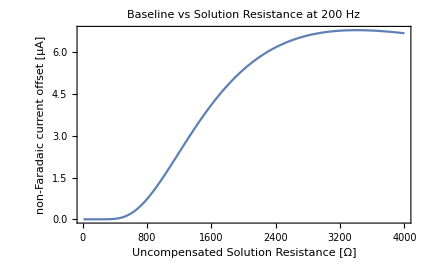

```mathematica
(* ===STEP 6:Current vs Solution Resistance at f=200 Hz===*)

analyticalBaselineExpression
fixedFrequency=200; (*Hz*)
assumedCapacitance = 412*10^-9;
analyticalBaselineExpressionExample = analyticalBaselineExpression/.{fSWV->fixedFrequency, CDL->assumedCapacitance}
Plot[10^6 analyticalBaselineExpressionExample, {Rsol,10,4000}, Frame->True, PlotLabel->"Baseline vs Solution Resistance at 200 Hz",FrameLabel->{"Uncompensated Solution Resistance [Ω]", "non-Faradaic current offset [µA]"}]
```

```mathematica
groupedWithFreq=Map[Thread[{frequencies,10^6 #}]&,(*or Transpose[{frequencies,#}]*)grouped1,{2}];
```

```mathematica
(* kD, ...*)
```

```mathematica
firstCurves=First/@groupedWithFreq;
deltaIwithNoResistor = firstCurves
```

<|0.→{{10,0.0722176212121212104},{15,0.172823761904761915},{20,0.296524844444444441},{25,0.432671460658083056},{30,0.567050085470085421},{40,0.830458675213675123},{70,1.43845592517006809},{80,1.58542167204301058},{100,1.65900008479999997},{200,2.28877739837398407},{300,2.62849462650602394},{400,2.84923104000000012},{500,2.87055397560975626},{600,2.9984089473684207}},0.00001→{{10,0.0687321545893719824},{15,0.165057777777777766},{20,0.284534018018017964},{25,0.416882249612403091},{30,0.54823272727272727},{40,0.805982383333333336},{70,1.40067414285714271},{80,1.54526053763440856},{100,1.61498872320000021},{200,2.2378909516129034},{300,2.56219207999999986},{400,2.78720039183673473},{500,2.80705769999999964},{600,2.92985436144578289}},0.00004→{{10,0.0662420461538461574},{15,0.158202914285714281},{20,0.273646625000000005},{25,0.401830505139500686},{30,0.531454312236286917},{40,0.786207322314049612},{70,1.3828405687074829},{80,1.53055963387978158},{100,1.60271955789473681},{200,2.22134827983539103},{300,2.55635179032258024},{400,2.77687897580645171},{500,2.78088039166666622},{600,2.92198470967741973}},0.0001→{{10,0.0632285000000000027},{15,0.149849842857142832},{20,0.260939962962962933},{25,0.384368837681159448},{30,0.51152148717948714},{40,0.76507880341880323},{70,1.36368666666666668},{80,1.5209946051912568},{100,1.59396628273092377},{200,2.23314093117408919},{300,2.57039273895582301},{400,2.7969175421686745},{500,2.81179918072289212},{600,2.96364597540983637}},0.00032→{{10,0.0575172916666666729},{15,0.134485314285714275},{20,0.235760202898550741},{25,0.353372242152466381},{30,0.478031636363636331},{40,0.731834475592747558},{70,1.36297330612244905},{80,1.52298755913978494},{100,1.60497036706827346},{200,2.28390541463414668},{300,2.64046099200000034},{400,2.87761058064516131},{500,2.90686632000000029},{600,3.04579652500000012}},0.0093→{{10,0.0334508906250000131},{15,0.0716702769230769459},{20,0.12609439215686273},{25,0.196713217948717945},{30,0.28704172972972977},{40,0.512764548022598866},{70,1.34103457006802733},{80,1.60858775416666664},{100,1.77530183801652907},{200,3.05266018032786907},{300,3.71954326907630525},{400,4.14356252459016388},{500,4.18478219433198497},{600,4.41853195102040809}}|>

```mathematica
ModelFunction[frequency_,concentration_,params_Association]:=
Module[
{theta,RctEff,t1Local,expr},
theta=concentration/(params["kD"]+concentration);
RctEff=1/((1-theta)/params["Rct0"]+theta/params["Rct1"]);
t1Local=1/(2*frequency);
expr=analyticalCHICurrentExpression/. {CDL->params["CDL"],Rsol->params["Rsol"],Capt->params["Capt"],Rct->RctEff,t1->t1Local, fSWV->frequency};
expr
];


(*STEP 3:Define FitFunction*)
FitFunction[allData_List,constants_Association,initialGuesses_Association,fitVariables_List]:=
Module[
{modelFunc,fit,result},
modelFunc[f_,c_,rct0_,rct1_,kD_,capt_]:=ModelFunction[f,c,Join[constants,<|"Rct0"->rct0,"Rct1"->rct1,"kD"->kD,"Capt"->capt|>]];
fit=FindFit[
allData,
modelFunc[f,c,rct0,rct1,kD,capt],
{{rct0,initialGuesses["Rct0"],100,50000},{rct1,initialGuesses["Rct1"],100,50000},{kD,initialGuesses["kD"],1*10^-5,10^-1},{capt,initialGuesses["Capt"],1*10^-8,1*10^-5}},
{f,c},
(* Method->{"NMinimize"}, *)
Method->"LevenbergMarquardt",
AccuracyGoal->6,
PrecisionGoal->6,
MaxIterations->5000
];
result=Join[constants,<|"Rct0"->(rct0/. fit),"Rct1"->(rct1/. fit),"kD"->(kD/. fit),"Capt"->(capt/. fit)|>];
result];

(*flatten all data*)



(* 
allData=Flatten[KeyValueMap[Function[{conc,curve},curve/. {f_,IμA_}:>{f,conc,IμA*10^-6}],deltaIwithNoResistor],1]; 
filteredData=allData; *)


(* 
 filteredData=Select[allData,#[[1]]>=20&]; 
filteredData=Select[filteredData,#[[2]]>=0.0005&] 
filteredData=Select[filteredData,#[[2]]<0.00001&] (* select only zero *)
*)

(*---Flatten Association into {f,c,I} with I in Amps---*)
allData=Flatten[KeyValueMap[Function[{conc,curve},curve/. {f_,IuA_}:>{f,conc,IuA*10^-6}],deltaIwithNoResistor],1];

(*---Filtering pipeline (edit these rules as needed)---*)
filteredData=allData;

(*Example:keep only f>=20 Hz*)
filteredData=Select[filteredData,#[[1]]>=0.001&];

(*Example:keep only concentrations>=0.0005 M*)
(* filteredData=Select[filteredData,#[[2]]==0&] *)


constants=<|"CDL"->CdlEIS,"Rsol"->RsEIS       (*example;replace with your known/assumed value*)|>;



initialGuesses=<|"Rct0"->15000,"Rct1"->5000,"kD"->2*10^-3,"Capt"->8.7*10^-7|>;

fitVariables={"Rct0","Rct1","kD"};

result=FitFunction[filteredData,constants,initialGuesses,fitVariables];

Print["Fitted parameters:"];
Print[result];
```

Fitted parameters:

<|CDL→71/200000000,Rsol→294,Rct0→17034.,Rct1→6542.44,kD→0.0171989,Capt→2.27651×10^-7|>

```mathematica
{t,fitResult}=AbsoluteTiming[FitFunction[filteredData,constants,initialGuesses,fitVariables]];


Print["The function evaluated in t = ", 1000*t , " milliseconds" ]
```

The function evaluated in t = 282.08 milliseconds

General::munfl: Exp[-1916.26] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2039.56] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1277.51] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

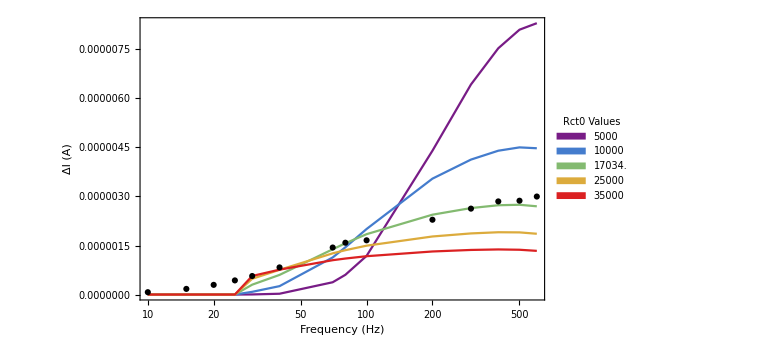

```mathematica
(*Find lowest concentration*)
uniqueConcs=DeleteDuplicates[filteredData[[All,2]]];
minConc=Min[uniqueConcs];

(*Extract data at lowest concentration*)
lowestConcData=Select[filteredData,#[[2]]==minConc&];

(*Extract fitted parameters*)
rct0Fit=result["Rct0"];
rct1Fit=result["Rct1"];
kDFit=result["kD"];
captFit=result["Capt"];

(*Define range of Rct0 values around fit*)
rct0Values={5000,10000,rct0Fit,25000,35000};

(*Define legend labels*)
legendLabels=ToString[NumberForm[#,{6,0}]]&/@rct0Values;

(*Generate rainbow colors*)
colors=ColorData["Rainbow"]/@Rescale[Range[Length[rct0Values]],{1,Length[rct0Values]}];

(*Frequencies to evaluate theory curves*)
frequencies=Sort[lowestConcData[[All,1]]];

(*Generate theory curves as lists of points*)
theoryCurves=Table[Table[{f,ModelFunction[f,minConc,Join[constants,<|"Rct0"->rct0Values[[i]],"Rct1"->rct1Fit,"kD"->kDFit,"Capt"->captFit|>]]},{f,frequencies}],{i,Length[rct0Values]}];

(*Make the theory plot*)
theoryPlot=ListLogLinearPlot[theoryCurves,PlotStyle->(Directive[#,Thick]&/@colors),Joined->True,PlotMarkers->None,Frame->True,FrameLabel->{"Frequency (Hz)","ΔI (A)"},PlotLegends->Placed[SwatchLegend[colors,legendLabels,LegendLabel->"Rct0 Values"],Right],ImageSize->Large];

(*Plot the experimental data*)
expPlot=ListLogLinearPlot[{lowestConcData[[All,{1,3}]]},PlotStyle->{Black},PlotMarkers->{Automatic},Joined->False];

(*Combine plots*)
Show[theoryPlot,expPlot,PlotRange->All]
```

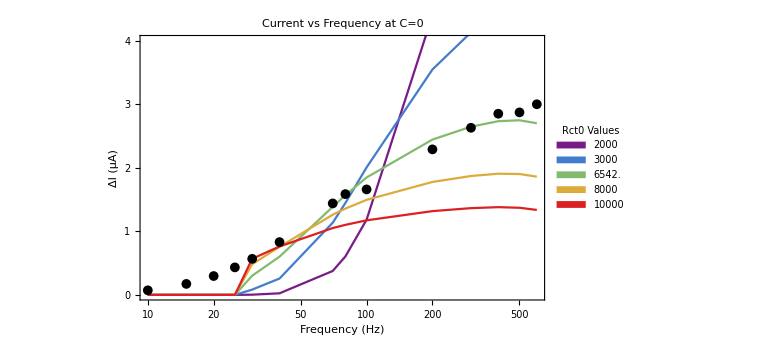

```mathematica
makeOutsideTicksCustom[vals_]:=Table[{x,ToString[x],{0,0.02}},{x,vals}];

makeOutsideLogTicks[min_,max_]:=Module[{major},major=10^Range[Ceiling[Log10[min]],Floor[Log10[max]]];
({#,Superscript[10,Log10[#]],{0,0.02}}&)/@major];

(*Same data,converted to microamps*)
theoryCurvesMicroA=Map[{#[[1]],10^6 #[[2]]}&,theoryCurves,{2}];

expDataMicroA=({#[[1]],10^6 #[[2]]}&)/@lowestConcData[[All,{1,3}]];

theoryPlot=ListLogLinearPlot[theoryCurvesMicroA,PlotStyle->(Directive[#,Thick]&/@colors),Joined->True,PlotMarkers->None,Frame->True,Axes->False,FrameLabel->{Style["Frequency (Hz)",16,Bold],Style["ΔI (µA)",16,Bold]},FrameTicks->{{makeOutsideTicksCustom[{0,1,2,3,4}],None},{makeOutsideLogTicks[Min[frequencies],Max[frequencies]],None}},FrameTicksStyle->Directive[FontFamily->"Helvetica",FontSize->14,Black],PlotLegends->Placed[SwatchLegend[colors,legendLabels,LegendLabel->Style["Rct0 Values",14]],Right],ImageSize->Large];

expPlot=ListLogLinearPlot[{expDataMicroA},PlotStyle->{Black},PlotMarkers->{Automatic,10},Joined->False];

publicationFigureRct0Sensitivity=Show[theoryPlot,expPlot,PlotRange->{{All,All},{0,4}},PlotLabel->Style["Current vs Frequency at C=0",18,Bold]];

publicationFigureRct0Sensitivity
```

```mathematica
Export["publicationFigureRct0Sensitivity.png",publicationFigureRct0Sensitivity,ImageResolution->600]
```

publicationFigureRct0Sensitivity.png

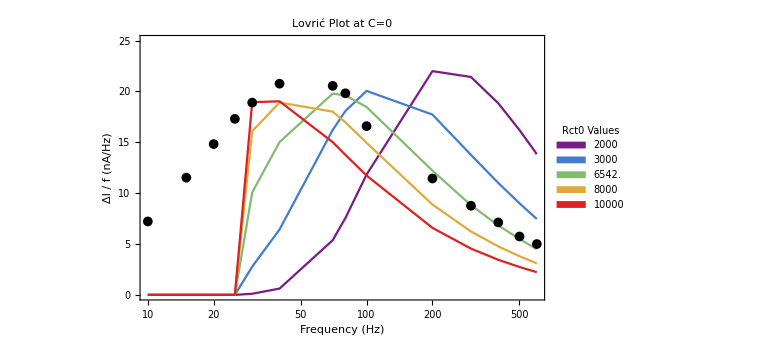

```mathematica
(*Lovric plot:same curves,y=current/frequency*)
theoryCurvesLovric=Map[{#[[1]],10^9 #[[2]]/#[[1]]}&,theoryCurves,{2}];

expDataLovric=({#[[1]],10^9 #[[2]]/#[[1]]}&)/@lowestConcData[[All,{1,3}]];

lovricYMax=0.1 Ceiling[10 Max[Join[Flatten[theoryCurvesLovric[[All,All,2]]],expDataLovric[[All,2]]]]];
lovricYMax=25;
lovricYTicks=Range[0,lovricYMax,lovricYMax/5];

lovricTheoryPlot=ListLogLinearPlot[theoryCurvesLovric,PlotStyle->(Directive[#,Thick]&/@colors),Joined->True,PlotMarkers->None,Frame->True,Axes->False,FrameLabel->{Style["Frequency (Hz)",16,Bold],Style["ΔI / f  (nA/Hz)",16,Bold]},FrameTicks->{{makeOutsideTicksCustom[lovricYTicks],None},{makeOutsideLogTicks[Min[frequencies],Max[frequencies]],None}},FrameTicksStyle->Directive[FontFamily->"Helvetica",FontSize->14,Black],PlotLegends->Placed[SwatchLegend[colors,legendLabels,LegendLabel->Style["Rct0 Values",14]],Right],ImageSize->Large];

lovricExpPlot=ListLogLinearPlot[{expDataLovric},PlotStyle->{Black},PlotMarkers->{Automatic,10},Joined->False];

publicationFigureLovric=Show[lovricTheoryPlot,lovricExpPlot,PlotRange->{{All,All},{0,lovricYMax}},PlotLabel->Style["Lovrić Plot at C=0",18,Bold]];

publicationFigureLovric
```

```mathematica
combinedFigure=GraphicsRow[{Show[publicationFigureRct0Sensitivity,ImageSize->400,ImagePadding->{{80,20},{65,25}}],Show[publicationFigureLovric,ImageSize->400,ImagePadding->{{80,20},{65,25}}]},Spacings->0.25,Background->White,ImageSize->1000];

combinedFigure
```

-Graphics-

```mathematica
Export["publicationFigurecombinedFigureLovric.png",combinedFigure,ImageResolution->600]
```

publicationFigurecombinedFigureLovric.png

General::munfl: Exp[-1916.26] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2048.72] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1277.51] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

$Aborted

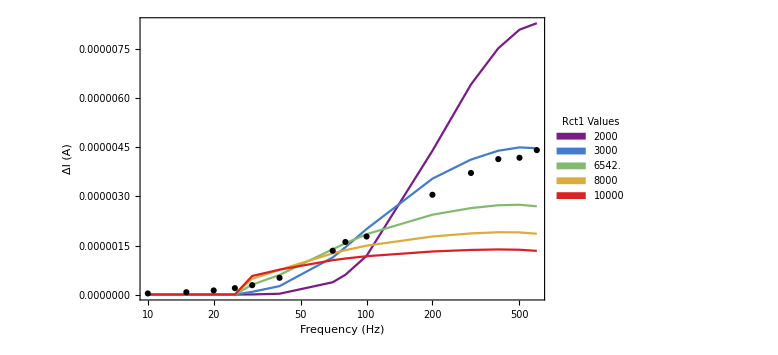

```mathematica
(*Find lowest concentration*)
uniqueConcs=DeleteDuplicates[filteredData[[All,2]]];
maxConc=Max[uniqueConcs];

(*Extract data at lowest concentration*)
highestConcData=Select[filteredData,#[[2]]==maxConc&];

(*Extract fitted parameters*)
rct0Fit=result["Rct0"];
rct1Fit=result["Rct1"];
kDFit=result["kD"];
captFit=result["Capt"];

(*Define range of Rct0 values around fit*)
rct1Values={2000,3000,rct1Fit,8000,10000};

(*Define legend labels*)
legendLabels=ToString[NumberForm[#,{6,0}]]&/@rct1Values;

(*Generate rainbow colors*)
colors=ColorData["Rainbow"]/@Rescale[Range[Length[rct1Values]],{1,Length[rct0Values]}];

(*Frequencies to evaluate theory curves*)
frequencies=Sort[highestConcData[[All,1]]];

(*Generate theory curves as lists of points*)
theoryCurves=Table[Table[{f,ModelFunction[f,maxConc,Join[constants,<|"Rct0"->rct0Fit,"Rct1"->rct1Values[[i]],"kD"->kDFit,"Capt"->captFit|>]]},{f,frequencies}],{i,Length[rct1Values]}];

(*Make the theory plot*)
theoryPlot=ListLogLinearPlot[theoryCurves,PlotStyle->(Directive[#,Thick]&/@colors),Joined->True,PlotMarkers->None,Frame->True,FrameLabel->{"Frequency (Hz)","ΔI (A)"},PlotLegends->Placed[SwatchLegend[colors,legendLabels,LegendLabel->"Rct1 Values"],Right],ImageSize->Large];

(*Plot the experimental data*)
expPlot=ListLogLinearPlot[{highestConcData[[All,{1,3}]]},PlotStyle->{Black},PlotMarkers->{Automatic},Joined->False];

(*Combine plots*)
Show[theoryPlot,expPlot,PlotRange->All]
```

General::munfl: Exp[-1916.26] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1989.59] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1277.51] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

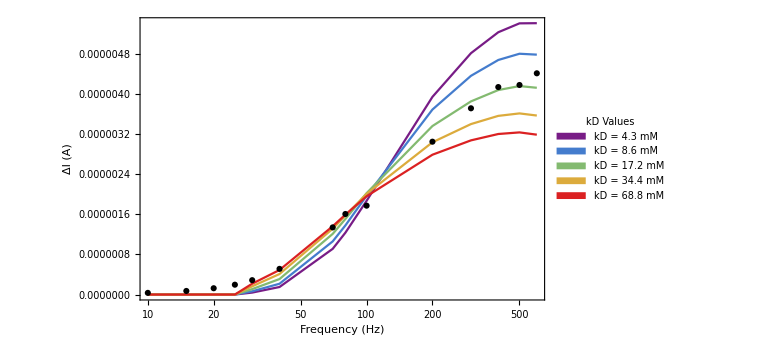

```mathematica
(*Find lowest concentration*)
uniqueConcs=DeleteDuplicates[filteredData[[All,2]]];
maxConc=Max[uniqueConcs];

(*Extract data at lowest concentration*)
highestConcData=Select[filteredData,#[[2]]==maxConc&];

(*Extract fitted parameters*)
rct0Fit=result["Rct0"];
rct1Fit=result["Rct1"];
kDFit=result["kD"];
captFit=result["Capt"];

(*Define range of Rct0 values around fit*)
kDValues={kDFit/4,kDFit/2,kDFit,2*kDFit,4*kDFit};

(*Define legend labels*)
legendLabels=("kD = "<>ToString[NumberForm[1000*#,{6,1}]]<>" mM")&/@kDValues;


(*Generate rainbow colors*)
colors=ColorData["Rainbow"]/@Rescale[Range[Length[kDValues]],{1,Length[kDValues]}];

(*Frequencies to evaluate theory curves*)
frequencies=Sort[highestConcData[[All,1]]];

(*Generate theory curves as lists of points*)
theoryCurves=Table[Table[{f,ModelFunction[f,maxConc,Join[constants,<|"Rct0"->rct0Fit,"Rct1"->rct1Fit,"kD"->kDValues[[i]],"Capt"->captFit|>]]},{f,frequencies}],{i,Length[rct1Values]}];

(*Make the theory plot*)
theoryPlot=ListLogLinearPlot[theoryCurves,PlotStyle->(Directive[#,Thick]&/@colors),Joined->True,PlotMarkers->None,Frame->True,FrameLabel->{"Frequency (Hz)","ΔI (A)"},PlotLegends->Placed[SwatchLegend[colors,legendLabels,LegendLabel->"kD Values"],Right],ImageSize->Large];

(*Plot the experimental data*)
expPlot=ListLogLinearPlot[{highestConcData[[All,{1,3}]]},PlotStyle->{Black},PlotMarkers->{Automatic},Joined->False];

(*Combine plots*)
Show[theoryPlot,expPlot,PlotRange->All]
```

{1.×10^-6,1.25893×10^-6,1.58489×10^-6,1.99526×10^-6,2.51189×10^-6,3.16228×10^-6,3.98107×10^-6,5.01187×10^-6,6.30957×10^-6,7.94328×10^-6,0.00001,0.0000125893,0.0000158489,0.0000199526,0.0000251189,0.0000316228,0.0000398107,0.0000501187,0.0000630957,0.0000794328,0.0001,0.000125893,0.000158489,0.000199526,0.000251189,0.000316228,0.000398107,0.000501187,0.000630957,0.000794328,0.001,0.00125893,0.00158489,0.00199526,0.00251189,0.00316228,0.00398107,0.00501187,0.00630957,0.00794328,0.01,0.0125893,0.0158489,0.0199526,0.0251189,0.0316228,0.0398107,0.0501187,0.0630957,0.0794328,0.1}

<|CDL→71/200000000,Rsol→294,Rct0→17034.,Rct1→6542.44,kD→kDval,Capt→2.27651×10^-7|>

{{0.,2.62849462650602394×10^-6},{0.00001,2.56219207999999987×10^-6},{0.00004,2.55635179032258024×10^-6},{0.0001,2.57039273895582301×10^-6},{0.00032,2.64046099200000034×10^-6},{0.0093,3.71954326907630525×10^-6}}

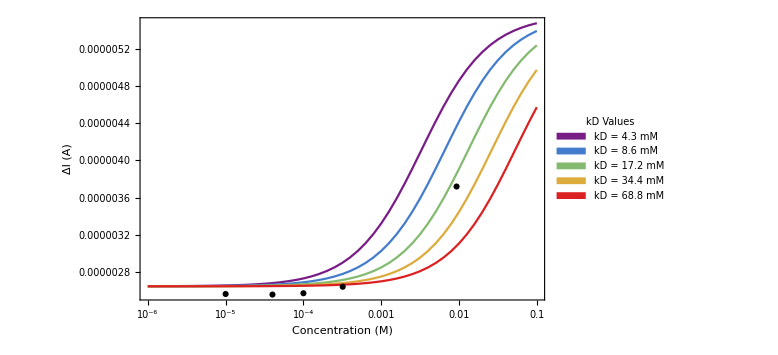

```mathematica
(*-------------------------------------------*)(*Set frequency for plotting ΔI vs conc*)(*-------------------------------------------*)
fPlot=300;  (*e.g.100 Hz*)

(*Define concentration range for x-axis*)
concRange=Table[10^x,{x,Log10[1*10^-6],Log10[1*10^-1],0.1}]

(*Extract fitted parameters*)
rct0Fit=result["Rct0"];
rct1Fit=result["Rct1"];
kDFit=result["kD"];
captFit=result["Capt"];

(*Define range of kD values around fit*)
kDValues={kDFit/4,kDFit/2,kDFit,2*kDFit,4*kDFit};

(*Define legend labels in mM*)
legendLabels=("kD = "<>ToString[NumberForm[1000*#,{6,1}]]<>" mM")&/@kDValues;

(*Generate rainbow colors*)
colors=ColorData["Rainbow"]/@Rescale[Range[Length[kDValues]],{1,Length[kDValues]}];

Join[constants,<|"Rct0"->rct0Fit,"Rct1"->rct1Fit,"kD"->kDval,"Capt"->captFit|>]

(*Generate theory curves:ΔI vs conc for each kD*)
theoryCurves=Table[Table[{conc,ModelFunction[fPlot,conc,Join[constants,<|"Rct0"->rct0Fit,"Rct1"->rct1Fit,"kD"->kDval,"Capt"->captFit|>]]},{conc,concRange}],{kDval,kDValues}];

(*Make the theory plot*)
theoryPlot=ListLogLinearPlot[theoryCurves,PlotStyle->(Directive[#,Thick]&/@colors),Joined->True,PlotMarkers->None,Frame->True,FrameLabel->{"Concentration (M)","ΔI (A)"},PlotLegends->Placed[SwatchLegend[colors,legendLabels,LegendLabel->"kD Values"],Right],ImageSize->Large, PlotRange->{Automatic,{0,Automatic}}];

(*-------------------------------------------------------------*)
(*Plot experimental data as ΔI vs conc at the chosen frequency*)
(*-------------------------------------------------------------*)

(*Extract unique concentrations from data*)
uniqueConcs=DeleteDuplicates[filteredData[[All,2]]];

(*Select only data at chosen frequency*)
expDataAtFreq=Select[filteredData,#[[1]]==fPlot&];

(*Extract {conc,ΔI} pairs*)
expPoints=expDataAtFreq[[All,{2,3}]]

(*Plot experimental data*)
expPlot=ListLogLinearPlot[{expPoints},PlotStyle->{Black},PlotMarkers->{Automatic},Joined->False, PlotRange->{Automatic,{0,Automatic}}];

(*Combine plots*)
Show[theoryPlot,expPlot,PlotRange->{Automatic,{0,Automatic}}]
```

General::munfl: Exp[-766.504] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-780.098] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-766.504] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

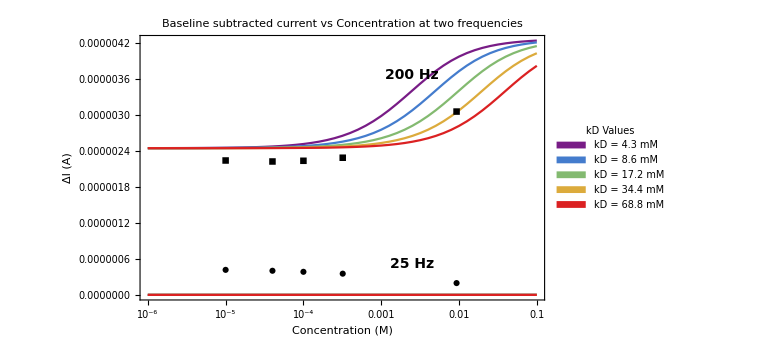

```mathematica
(*Define the frequencies you want plotted*)
fPlot={25,200};

(*Define concentration range*)
concRange=Table[10^x,{x,Log10[1*10^-6],Log10[1*10^-1],0.1}];

(*Extract fitted parameters*)
rct0Fit=result["Rct0"];
rct1Fit=result["Rct1"];
kDFit=result["kD"];
captFit=result["Capt"];

(*Define range of kD values around the fit*)
kDValues={kDFit/4,kDFit/2,kDFit,2*kDFit,4*kDFit};

(*Generate legend labels in mM*)
legendLabels=("kD = "<>ToString[NumberForm[1000*#,{6,1}]]<>" mM")&/@kDValues;

(*Generate rainbow colors for the different kD curves*)
colors=ColorData["Rainbow"]/@Rescale[Range[Length[kDValues]],{1,Length[kDValues]}];

(*------------------------------------------------------------*)
(*Compute theory curves for all frequencies and kD values*)
(*------------------------------------------------------------*)

(*Will store curves for each freq and kD value*)
theoryCurvesAll=Flatten[Table[Table[Table[{conc,ModelFunction[f,conc,Join[constants,<|"Rct0"->rct0Fit,"Rct1"->rct1Fit,"kD"->kDval,"Capt"->captFit|>]]},{conc,concRange}],{kDval,kDValues}],{f,fPlot}],1];

(*We’ll build plot styles to distinguish frequencies and kD*)

(*There are Length(kDValues) curves per frequency*)
freqStyles={Solid,Solid};  (*e.g.one style per frequency*)

plotStyles=Flatten[Table[Directive[colors[[k]],freqStyles[[fIndex]],Thick],{fIndex,Length[fPlot]},{k,Length[kDValues]}],1];

(*------------------------------------------------------------*)
(*Experimental data for both frequencies*)
(*------------------------------------------------------------*)

(*Separate experimental points by frequency*)
expDataByFreq=Table[Select[filteredData,#[[1]]==f&][[All,{2,3}]],{f,fPlot}];

(*Compute label positions*)
labelPrimitives=Table[Module[{data,meanX,maxY,labelPos},data=expDataByFreq[[i]];
If[Length[data]>0,meanX=Mean[data[[All,1]]];
maxY=Max[data[[All,2]]];
labelPos={meanX-6,maxY*1.2};(*place label 10% above max*)Text[Style[ToString[fPlot[[i]]]<>" Hz",Black,Bold,14],labelPos],Nothing]],{i,Length[fPlot]}];

(*------------------------------------------------------------*)
(*Plot everything together*)
(*------------------------------------------------------------*)

combinedPlot=Show[ListLogLinearPlot[theoryCurvesAll,PlotStyle->plotStyles,Joined->True,PlotMarkers->None,Frame->True,FrameLabel->{"Concentration (M)","ΔI (A)"},PlotRange->{Automatic,{0,Automatic}},PlotLabel->"Baseline subtracted current vs Concentration at two frequencies",PlotLegends->Placed[SwatchLegend[plotStyles[[1;;Length[kDValues]]],legendLabels,LegendLabel->"kD Values"],Right],ImageSize->Large],ListLogLinearPlot[expDataByFreq,PlotStyle->{Black,Black},PlotMarkers->{Automatic},Joined->False],Graphics[labelPrimitives],PlotRange->{Automatic,{0,Automatic}}];

combinedPlot
```

```mathematica
filteredData;
```

```mathematica
constants2=ReplacePart[constants, "Rsol"->2000]
```

<|CDL→71/200000000,Rsol→2000|>

```mathematica
<|"CDL"->71/200000000,"Rsol"->2000|>
```

<|CDL→71/200000000,Rsol→2000|>

```mathematica
constants2=constants
```

<|CDL→71/200000000,Rsol→294|>

General::munfl: Exp[-1916.26] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1950.24] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1916.26] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

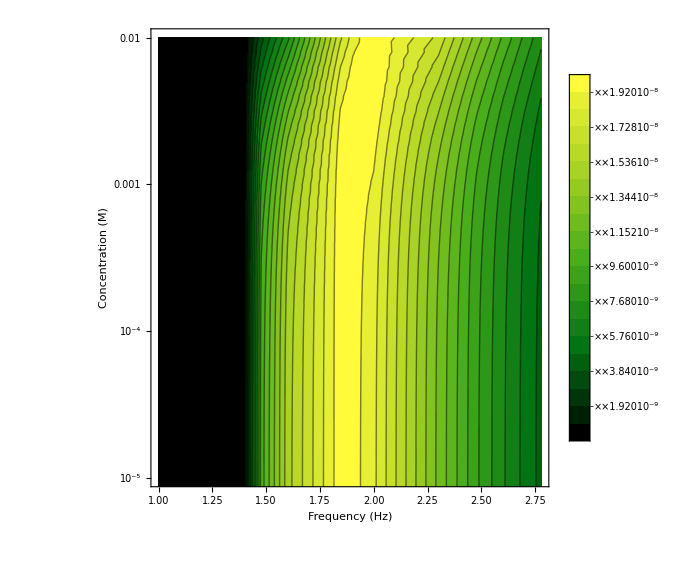

```mathematica
(* =============================================*)(*Contour plot:Frequency (x),Concentration (y),Color=ΔI*)(* =============================================*)(*1. Use all experimental frequencies as the x-grid*)
freqGrid=Union[filteredData[[All,1]]];

(*2. Use your existing concentration grid*)

concGridCeil=Select[concRange,#<=0.01&];

(*3. Extract fitted parameters and build a parameter association*)
rct0Fit=result["Rct0"];
rct1Fit=result["Rct1"];
kDFit=result["kD"];
captFit=result["Capt"];

paramsFit=Join[constants2,<|"Rct0"->rct0Fit,"Rct1"->rct1Fit,"kD"->kDFit,"Capt"->captFit|>];

(*4. Build raw (f,c,current) triples for ListContourPlot*)
dataTriples=Flatten[Table[{freqGrid[[i]],concGridCeil[[j]],ModelFunction[freqGrid[[i]],concGridCeil[[j]],paramsFit]/freqGrid[[i]]},{i,Length[freqGrid]},{j,Length[concGridCeil]}],1];
dataTriplesLog=dataTriples/. {f_,c_,z_}:>{Log10[f],c,z};

(*5. Make the contour plot*)
LovricContourPlotTheory=ListContourPlot[dataTriplesLog,Frame->True,FrameLabel->{"Frequency (Hz)","Concentration (M)"},PlotLegends->Automatic,ColorFunction->"AvocadoColors",Contours->20,InterpolationOrder->2,PlotRange->{Automatic,{10^-5,10^-2}},ScalingFunctions->{"Linear","Log"},(*log-y concentration axis*)ImageSize->Large];

LovricContourPlotTheory
```

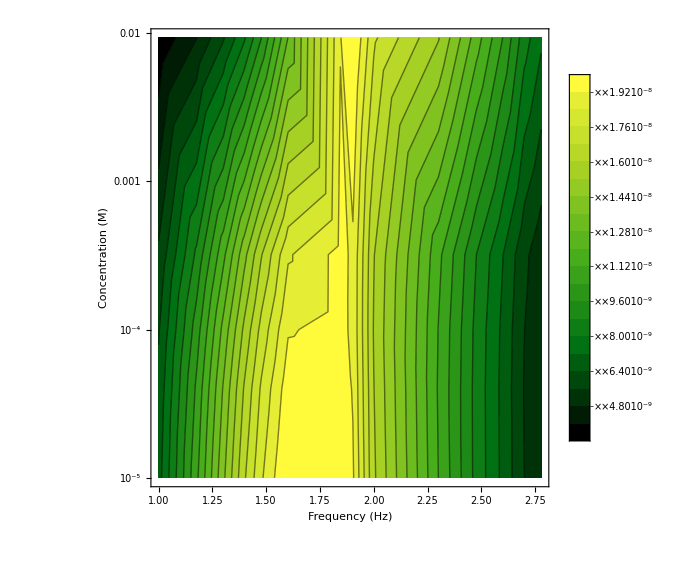

```mathematica
(* =============================================*)(*Experimental Lovric-type surface from filteredData*)(*x:Frequency (Hz,log axis),y:Concentration (M,log axis),z:I/f*)(* =============================================*)(*filteredData is of the form:{freq,conc,current}*)(*1. Build (f,c,I/f) triples*)
dataTriplesExp=filteredData/. {f_,c_,cur_}:>{f,c,cur/f};

(*2. Log-transform frequency for plotting on log-x axis*)
dataTriplesExpLog=dataTriplesExp/. {f_,c_,z_}:>{Log10[f],c,z};

(*3. Make the contour plot*)
expContourPlot=ListContourPlot[dataTriplesExpLog,Frame->True,FrameLabel->{"Frequency (Hz)","Concentration (M)"},PlotLegends->Automatic,ColorFunction->"AvocadoColors",Contours->20,InterpolationOrder->2,PlotRange->All,ScalingFunctions->{"Linear","Log"},(*log-y concentration axis*)ImageSize->Large];

expContourPlot
```

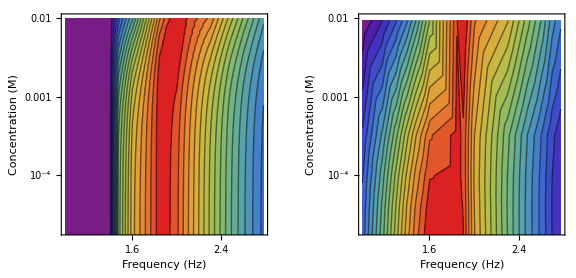

```mathematica
(* =============================================*)(*Side-by-side Lovric surfaces with preserved axes*)(* =============================================*)(*Extract underlying x,y ranges from your log-transformed data*)
xMin=Min[Join[dataTriplesLog[[All,1]],dataTriplesExpLog[[All,1]]]];
xMax=Max[Join[dataTriplesLog[[All,1]],dataTriplesExpLog[[All,1]]]];

yMin=Min[Join[dataTriplesLog[[All,2]],dataTriplesExpLog[[All,2]]]];
yMax=Max[Join[dataTriplesLog[[All,2]],dataTriplesExpLog[[All,2]]]];

commonXY={{xMin,xMax},{yMin,yMax}};

(*Rebuild the plots with enforced x/y PlotRange,preserving all formatting*)
theoryAligned=ListContourPlot[dataTriplesLog,Frame->True,FrameLabel->{"Frequency (Hz)","Concentration (M)"},ScalingFunctions->{"Linear","Log"},ColorFunction->"Rainbow",Contours->20,InterpolationOrder->2,PlotRange->{commonXY[[1]],commonXY[[2]],All},ImageSize->400];

expAligned=ListContourPlot[dataTriplesExpLog,Frame->True,FrameLabel->{"Frequency (Hz)","Concentration (M)"},ScalingFunctions->{"Linear","Log"},ColorFunction->"Rainbow",Contours->20,InterpolationOrder->2,PlotRange->{commonXY[[1]],commonXY[[2]],All},ImageSize->400];

(*Side-by-side comparison*)
GraphicsRow[{theoryAligned,expAligned},ImageSize->Large]
```

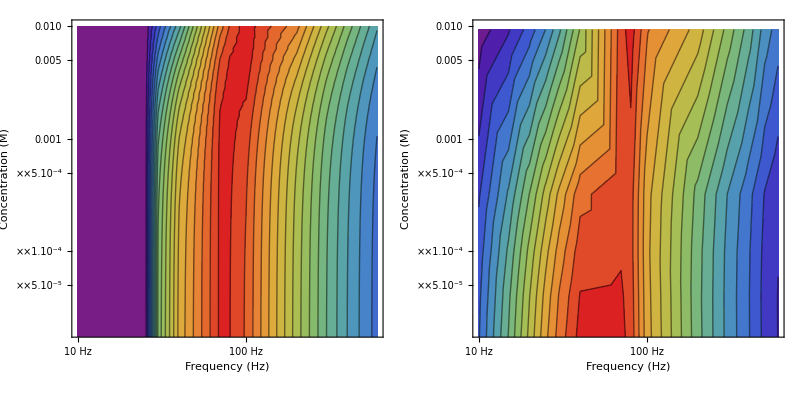

```mathematica
(*Ranges from your transformed data*)xMin=Min[Join[dataTriplesLog[[All,1]],dataTriplesExpLog[[All,1]]]];
xMax=Max[Join[dataTriplesLog[[All,1]],dataTriplesExpLog[[All,1]]]];

yMin=Min[Join[dataTriplesLog[[All,2]],dataTriplesExpLog[[All,2]]]];
yMax=Max[Join[dataTriplesLog[[All,2]],dataTriplesExpLog[[All,2]]]];

commonXY={{xMin,xMax},{yMin,yMax}};

zMin=Min[Join[dataTriplesLog[[All,3]],dataTriplesExpLog[[All,3]]]];
zMax=Max[Join[dataTriplesLog[[All,3]],dataTriplesExpLog[[All,3]]]];

(*Actual frequencies present in the data*)
freqValues=Union[filteredData[[All,1]]];

(*Only show these three if they exist*)
freqTicksToShow={10,100,1000};

xTicks=({Log10[#],ToString[#]<>" Hz"}&)/@Select[freqTicksToShow,MemberQ[freqValues,#]&];

(*THEORY*)
theoryAligned=ListContourPlot[dataTriplesLog,Frame->True,FrameLabel->{"Frequency (Hz)","Concentration (M)"},ScalingFunctions->{"Linear","Log"},ColorFunction->"Rainbow",Contours->20,InterpolationOrder->2,PlotRange->{commonXY[[1]],commonXY[[2]],{zMin,zMax}},FrameTicks->{{Automatic,None},{xTicks,None}},ImageSize->400];

(*EXPERIMENT*)
expAligned=ListContourPlot[dataTriplesExpLog,Frame->True,FrameLabel->{"Frequency (Hz)","Concentration (M)"},ScalingFunctions->{"Linear","Log"},ColorFunction->"Rainbow",Contours->20,InterpolationOrder->2,PlotRange->{commonXY[[1]],commonXY[[2]],{zMin,zMax}},FrameTicks->{{Automatic,None},{xTicks,None}},ImageSize->400];

(*Get the image height of the contour plots*)


(*Build a vertically oriented colorbar graphic of matching height*)
colorBarGraphic=Graphics[Inset[BarLegend[{"Rainbow",{zMin,zMax}},LegendLabel->"ΔI (A)",LabelStyle->14 ]], ImageSize->100];


GraphicsRow[{theoryAligned,expAligned},Spacings->2]
```

```mathematica
theoryAligned=ListContourPlot[dataTriplesLog,Frame->True,FrameLabel->{"Frequency (Hz)","Concentration (M)"},ScalingFunctions->{"Linear","Log"},ColorFunction->"Rainbow",Contours->20,InterpolationOrder->2,PlotRange->{commonXY[[1]],commonXY[[2]],{zMin,zMax}},FrameTicks->{{Automatic,Automatic},{xTicks,xTicks}},PlotLegends->BarLegend[{"Rainbow",{zMin,zMax}}],ImageSize->400];

expAligned=ListContourPlot[dataTriplesExpLog,Frame->True,FrameLabel->{"Frequency (Hz)","Concentration (M)"},ScalingFunctions->{"Linear","Log"},ColorFunction->"Rainbow",Contours->20,InterpolationOrder->2,PlotRange->{commonXY[[1]],commonXY[[2]],{zMin,zMax}},FrameTicks->{{Automatic,Automatic},{xTicks,xTicks}},PlotLegends->BarLegend[{"Rainbow",{zMin,zMax}}],ImageSize->400];
GraphicsRow[{theoryAligned,expAligned},ImageSize->Large]
```

-Graphics-

{{10,0.,7.22176212121212105×10^-8},{15,0.,1.72823761904761915×10^-7},{20,0.,2.96524844444444441×10^-7},{25,0.,4.32671460658083056×10^-7},{30,0.,5.67050085470085421×10^-7},{40,0.,8.30458675213675123×10^-7},{70,0.,1.43845592517006809×10^-6},{80,0.,1.58542167204301058×10^-6},{100,0.,1.65900008479999997×10^-6},{200,0.,2.28877739837398407×10^-6},{300,0.,2.62849462650602394×10^-6},{400,0.,2.84923104000000012×10^-6},{500,0.,2.87055397560975626×10^-6},{600,0.,2.9984089473684207×10^-6}}

2.27651×10^-7

General::munfl: Exp[-1916.26] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1970.15] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1277.51] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1916.26] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1950.23] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1277.51] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

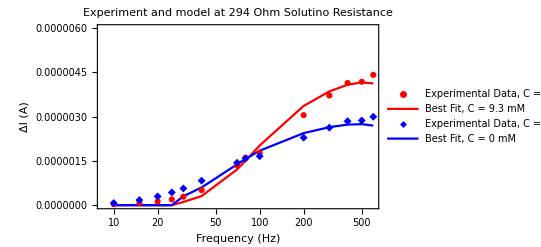

```mathematica
(*Find highest concentration*)
uniqueConcs=DeleteDuplicates[filteredData[[All,2]]];
maxConc=Max[uniqueConcs];

(*Extract data at highest concentration*)
lowestConcData=Select[filteredData,#[[2]]==0.&]
highestConcData=Select[filteredData,#[[2]]==maxConc&];

(*Evaluate model at fitted parameters*)
rct0Fit=result["Rct0"];
rct1Fit=result["Rct1"];
kDFit=result["kD"];
captFit=result["Capt"]
modelCurve=Table[{f,ModelFunction[f,maxConc,Join[constants,<|"Rct0"->rct0Fit,"Rct1"->rct1Fit,"kD"->kDFit, "Capt"->captFit|>]]},{f,Sort[highestConcData[[All,1]]]}];
modelCurve2=Table[{f,ModelFunction[f,0,Join[constants,<|"Rct0"->rct0Fit,"Rct1"->rct1Fit,"kD"->kDFit, "Capt"->captFit|>]]},{f,Sort[highestConcData[[All,1]]]}];
(*Plot*)
ListLogLinearPlot[{highestConcData[[All,{1,3}]],modelCurve,lowestConcData[[All,{1,3}]],modelCurve2 },PlotStyle->{Red,Red, Blue, Blue},PlotMarkers->{Automatic,None},Joined->{False,True},PlotLegends->{"Experimental Data, C = 9.3 mM","Best Fit, C = 9.3 mM", "Experimental Data, C = 0 mM","Best Fit, C = 0 mM"},Frame->True,FrameLabel->{"Frequency (Hz)","ΔI (A)"},PlotLabel->Row[{"Experiment and model at 294 Ohm Solutino Resistance"}], PlotRange->{Automatic,{0,6*10^-6}}]
```

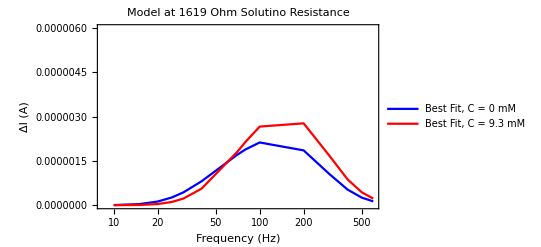

```mathematica
(* Generate simulated data for increased resistance! *)
constants2=ReplacePart[constants,"Rsol"->1619];

(* assume R = *)
modelCurvewithTargethighRes=Table[{f,ModelFunction[f,maxConc,Join[constants2,<|"Rct0"->rct0Fit,"Rct1"->rct1Fit,"kD"->kDFit, "Capt"->captFit|>]]},{f,Sort[highestConcData[[All,1]]]}];
modelCurvenoTargethighRes=Table[{f,ModelFunction[f,0,Join[constants2,<|"Rct0"->rct0Fit,"Rct1"->rct1Fit,"kD"->kDFit, "Capt"->captFit|>]]},{f,Sort[highestConcData[[All,1]]]}];
ListLogLinearPlot[{modelCurvenoTargethighRes,modelCurvewithTargethighRes },PlotStyle->{Blue,Red, Blue, Blue},PlotMarkers->{None,None},Joined->{True,True},PlotLegends->{"Best Fit, C = 0 mM","Best Fit, C = 9.3 mM"},Frame->True,FrameLabel->{"Frequency (Hz)","ΔI (A)"},PlotLabel->Row[{"Model at 1619 Ohm Solutino Resistance"}], PlotRange->{Automatic,{0,6*10^-6}}]
(*Plot*)
```

```mathematica
ListLogLinearPlot[{highestConcData[[All,{1,3}]],modelCurve,lowestConcData[[All,{1,3}]],modelCurve2 },PlotStyle->{Red,Red, Blue, Blue},PlotMarkers->{Automatic,None},Joined->{False,True},PlotLegends->{"Experimental Data, C = 9.3 mM","Best Fit, C = 9.3 mM", "Experimental Data, C = 0 mM","Best Fit, C = 0 mM"},Frame->True,FrameLabel->{"Frequency (Hz)","ΔI (A)"},PlotLabel->Row[{"Experiment and model at 294 Ohm Solutino Resistance"}], PlotRange->{Automatic,{0,6*10^-6}}]
```

-Graphics-

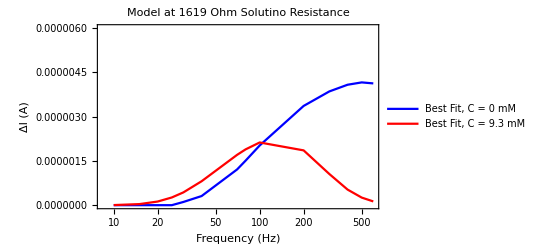

```mathematica
ListLogLinearPlot[{modelCurve, modelCurvenoTargethighRes },PlotStyle->{Blue,Red, Blue, Blue},PlotMarkers->{None,None},Joined->{True,True},PlotLegends->{"Best Fit, C = 0 mM","Best Fit, C = 9.3 mM"},Frame->True,FrameLabel->{"Frequency (Hz)","ΔI (A)"},PlotLabel->Row[{"Model at 1619 Ohm Solutino Resistance"}], PlotRange->{Automatic,{0,6*10^-6}}]
```

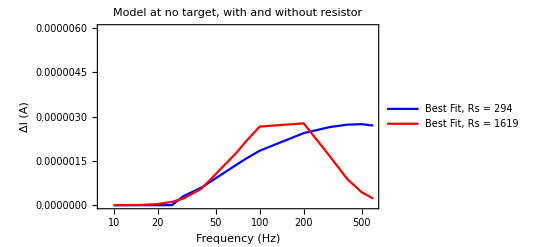

```mathematica
(* assume R = *)

ListLogLinearPlot[{modelCurve2, modelCurvewithTargethighRes },PlotStyle->{Blue,Red, Blue, Blue},PlotMarkers->{None,None},Joined->{True,True},PlotLegends->{"Best Fit, Rs = 294","Best Fit, Rs = 1619"},Frame->True,FrameLabel->{"Frequency (Hz)","ΔI (A)"},PlotLabel->Row[{"Model at no target, with and without resistor"}], PlotRange->{Automatic,{0,6*10^-6}}]
(*Plot*)
```

{{Conc,10,15,20,25,30,40,70,80,100,200,300,400,500,600},{0.,3.57169×10^-9,3.64749×10^-8,1.23312×10^-7,2.6127×10^-7,4.33272×10^-7,8.11539×10^-7,1.70601×10^-6,1.89134×10^-6,2.12646×10^-6,1.85824×10^-6,1.05695×10^-6,5.2854×10^-7,2.56875×10^-7,1.2746×10^-7},{0.00001,3.55542×10^-9,3.63691×10^-8,1.23063×10^-7,2.60892×10^-7,4.32822×10^-7,8.11149×10^-7,1.70653×10^-6,1.89215×10^-6,2.12771×10^-6,1.85986×10^-6,1.05797×10^-6,5.29088×10^-7,2.57154×10^-7,1.27605×10^-7},{0.00004,3.50721×10^-9,3.60542×10^-8,1.2232×10^-7,2.59761×10^-7,4.31475×10^-7,8.09979×10^-7,1.70805×10^-6,1.89455×10^-6,2.13147×10^-6,1.8647×10^-6,1.06104×10^-6,5.30727×10^-7,2.57992×10^-7,1.28039×10^-7},{0.0001,3.41331×10^-9,3.54362×10^-8,1.20856×10^-7,2.57524×10^-7,4.28804×10^-7,8.07641×10^-7,1.71103×10^-6,1.89929×10^-6,2.1389×10^-6,1.87433×10^-6,1.06715×10^-6,5.33991×10^-7,2.59659×10^-7,1.28903×10^-7},{0.00032,3.09585×10^-9,3.32978×10^-8,1.1572×10^-7,2.49598×10^-7,4.19249×10^-7,7.99088×10^-7,1.72136×10^-6,1.91592×10^-6,2.16531×10^-6,1.90899×10^-6,1.0892×10^-6,5.45793×10^-7,2.65696×10^-7,1.32032×10^-7},{0.0093,2.74414×10^-10,6.98718×10^-9,3.80229×10^-8,1.09003×10^-7,2.24015×10^-7,5.61572×10^-7,1.80158×10^-6,2.1479×10^-6,2.66489×10^-6,2.77524×10^-6,1.67872×10^-6,8.73583×10^-7,4.37569×10^-7,2.224×10^-7}}

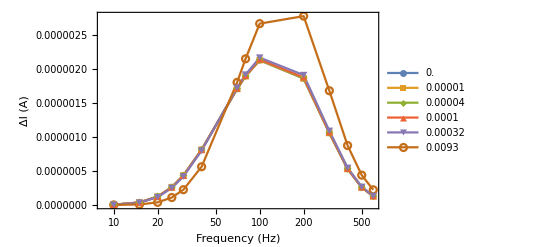

```mathematica
colHeadings=Prepend[frequencies,"Conc"];
uniqueConcs=DeleteDuplicates[concentrationList];

simRows=Table[Prepend[(ModelFunction[#,conc,Join[constants2,<|"Rct0"->rct0Fit,"Rct1"->rct1Fit,"kD"->kDFit,"Capt"->captFit|>]]&)/@frequencies,conc],{conc,uniqueConcs}];

simTable=Prepend[simRows,colHeadings]
ListLogLinearPlot[(Transpose[{frequencies,#}]&/@(Rest/@Rest[simTable])),Frame->True,FrameLabel->{"Frequency (Hz)","ΔI (A)"},Joined->True, PlotMarkers->Automatic,PlotRange->All,PlotLegends->simTable[[2;;,1]]]
```

```mathematica
(* NotebookDirectory[] *)
(* Export[FileNameJoin[{NotebookDirectory[],"simTable.csv"}],simTable,"CSV"] *)
```

```mathematica
(* now convert the best fit parameters into Butler Volmer paramaters!! *)
```

```mathematica
cleanSimTable=simTable/. x_?NumericQ:>N[x,10];

Export[FileNameJoin[{NotebookDirectory[],"simTable_clean.csv"}],cleanSimTable,"CSV"]
```

C:\Users\Bob Lansdorp\Documents\Wolfram Mathematica\aptamerModel\simTable_clean.csv

```mathematica
analyticalBaselineExpression
```

0.1 CDL ⅇ^(-2/(CDL fSWV Rsol)) (-1+ⅇ^(1/(4 CDL fSWV Rsol))) (-1+3 ⅇ^(1/(2 CDL fSWV Rsol))-4 ⅇ^(1/(CDL fSWV Rsol))+4 ⅇ^(3/(2 CDL fSWV Rsol))) fSWV

```mathematica
(* bonus: fit the non-faradaic baseline current increase to analytical theory: do Cdl and Rs match? *)




(* this section is optional... fit the added resistor data *)
(* note: there are some errors in the code below... it is using baseline fitting on non-baseline data  *)
experimentalDataWithResistor=Import["C:\\Users\\Bob Lansdorp\\Documents\\Wolfram Mathematica\\aptamerModel\\experimentalData\\2025-11-13\\E2Ir_vs_Freq10Hz_15Hz_20Hz_25Hz_30Hz_40Hz_70Hz_80Hz_100Hz_200Hz_300Hz_400Hz_500Hz_600Hz_.txt","Table"];
columnHeadersWithResistor=experimentalDataWithResistor[[1]];

frequencies=ToExpression[StringReplace[columnHeaders,"Current_"->""]];

(* use the know concentrations *)
concentrationList=Join[ConstantArray[0.0,4],ConstantArray[1.0*^-5,3],ConstantArray[4.0*^-5,3],ConstantArray[1.0*^-4,3],ConstantArray[3.2*^-4,3],ConstantArray[9.3*^-3,3]];

concentrationList=Take[concentrationList,Length[data1]];

grouped1=GroupBy[Thread[{concentrationList,data1}],First->Last];

(*STEP 2:Define ModelFunction*)
ModelFunctionNonFaradaic[frequency_,params_Association]:=Module[{t1Local,expr},
t1Local=1/(2*frequency);
expr=analyticalBaselineExpression/. {CDL->params["CDL"],Rsol->params["Rsol"],fSWV->frequency};
expr
];

(*STEP 3:Define FitFunction*)
FitNonFaradaicBaseline[data_,constants_Association,initialGuesses_Association,fitVariables_List]:=
Module[{modelFunc,fit,result},(*Define modelFunc as a function of the fit variables*)
modelFunc[f_,cdl_,rsol_]:=ModelFunctionNonFaradaic[f,Join[constants,<|"CDL"->cdl,"Rsol"->rsol|>]];

fit=FindFit[
data,
modelFunc[f,cdl,rsol],
{
{cdl,initialGuesses["CDL"],10^-7,10^-4},
{rsol,initialGuesses["Rsol"],10,50000}
},
f,
Method->{"NMinimize"},
AccuracyGoal->6,
PrecisionGoal->6,
MaxIterations->5000];

result=Join[constants,<|"CDL"->(cdl/. fit),"Rsol"->(rsol/. fit)|>];
result];

(*STEP 4:Example usage*)

(* data = experimentalDataWithResistor/. {f_,iμA_}:>{f,iμA*10^-6} *)
(* data=Select[data,#[[1]]>100&]; *)
data2=experimentalDataWithResistor[[2;;]];

grouped2=GroupBy[Thread[{concentrationList,data2}],First->Last];
groupedWithFreq2=Map[Thread[{frequencies,10^6 #}]&,(*or Transpose[{frequencies,#}]*)grouped2,{2}];


(* kD, ...*)


firstCurves2=First/@groupedWithFreq2;
deltaIwithResistor = firstCurves2


allData2=Flatten[KeyValueMap[Function[{conc,curve},curve/. {f_,IμA_}:>{f,conc,IμA*10^-6}],deltaIwithResistor],1]; 


(*build {f,conc,I(A)}*)
allData2=Flatten[KeyValueMap[Function[{conc,curve},curve/. {f_,IuA_}:>{f,conc,IuA*10^-6}],deltaIwithResistor],1];

(*choose only 0 M concentration and drop conc column->{f,I}*)
(*allData2 is {f,conc,I(A)}*)
dataBaseline=Select[allData2,Abs[#[[2]]-0.]<=10^-12&];

dataBaseline=dataBaseline[[All,{1,3}]]  (*drop concentration column->{f,I}*)



(*Fixed constants*)
constants=<||>

(*Initial guesses for fitted variables*)
initialGuesses=<|"CDL"->0.4*10^-6,"Rsol"->1500|>;
fitVariables={"CDL","Rsol"};

result=FitNonFaradaicBaseline[dataBaseline,constants,initialGuesses,fitVariables]

Print["Fitted parameters:"];
Print[result];
```

<|0.→{{10,0.253598617777777793},{15,0.550210418803418727},{20,0.854485616666666548},{25,1.15657299051490533},{30,1.41979699999999986},{40,1.9481537590361445},{70,3.15669634146341464},{80,3.47673506666666706},{100,3.65434768000000006},{200,4.82437792000000114},{300,4.59323728000000089},{400,3.79579560000000452},{500,3.42373180722891638},{600,2.74350526315789563}},0.00001→{{10,0.240968008771929812},{15,0.522725274261603458},{20,0.814108971193415528},{25,1.10494488843537408},{30,1.36336591566265046},{40,1.87842211466666707},{70,3.0631530894308947},{80,3.38574880000000046},{100,3.56111000000000037},{200,4.72713888000000045},{300,4.51529232000000072},{400,3.74091400000001017},{500,3.37583142857142961},{600,2.69321016949152712}},0.00004→{{10,0.231452587719298273},{15,0.500850632911392527},{20,0.782568658536585368},{25,1.06575167482993205},{30,1.32118968674698799},{40,1.83553170666666646},{70,3.03365533333333365},{80,3.36147924731182811},{100,3.54116879999999998},{200,4.72600736000000059},{300,4.50697344000000128},{400,3.72115072000000679},{500,3.35427480000000622},{600,2.6644472103004301}},0.0001→{{10,0.223041591397849435},{15,0.474893911392405098},{20,0.740467691358024787},{25,1.0154762423025435},{30,1.26677245783132517},{40,1.77944988172043038},{70,3.01279016260162577},{80,3.3416561290322581},{100,3.53001528000000003},{200,4.77313007999999994},{300,4.58550544000000149},{400,3.8094660800000037},{500,3.44259807228915722},{600,2.74815060728745448}},0.00032→{{10,0.20801666666666666},{15,0.434612283333333321},{20,0.681689146341463529},{25,0.944847273712737145},{30,1.1935916024096386},{40,1.71917138018741635},{70,3.02880197278911503},{80,3.38360354838709686},{100,3.59060816799999996},{200,4.94748207999999986},{300,4.79428376000000376},{400,4.00222136000000166},{500,3.62931485714285732},{600,2.93023333333333967}},0.0093→{{10,0.136039251366120226},{15,0.274214000000000023},{20,0.442493479166666657},{25,0.65376722222222205},{30,0.897603821138211512},{40,1.48947407526881731},{70,3.44854888435374169},{80,4.03761456989247448},{100,4.41581505600000055},{200,6.65493968000000123},{300,6.55223688000000305},{400,5.51945136000000678},{500,5.01375204819277271},{600,4.03566560000000837}}|>

{{10,2.53598617777777793×10^-7},{15,5.50210418803418727×10^-7},{20,8.54485616666666548×10^-7},{25,1.15657299051490533×10^-6},{30,1.41979699999999986×10^-6},{40,1.9481537590361445×10^-6},{70,3.15669634146341464×10^-6},{80,3.47673506666666706×10^-6},{100,3.65434768000000006×10^-6},{200,4.82437792000000114×10^-6},{300,4.59323728000000089×10^-6},{400,3.79579560000000452×10^-6},{500,3.42373180722891638×10^-6},{600,2.74350526315789563×10^-6}}

<||>

<|CDL→6.78172×10^-7,Rsol→12080.|>

Fitted parameters:

<|CDL→6.78172×10^-7,Rsol→12080.|>

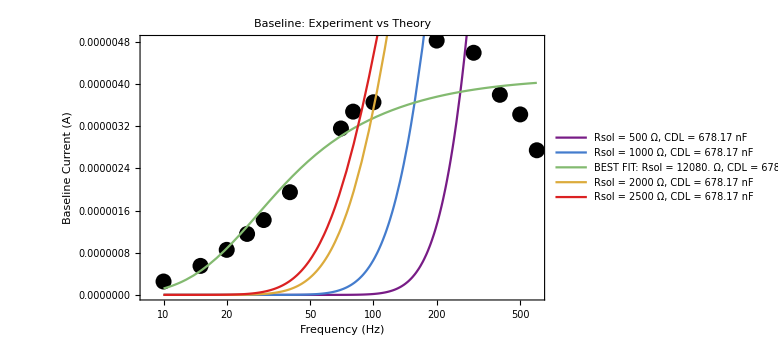

```mathematica
(*STEP 5:Experiment vs theory plot (baseline only)*)(*convenience:swap only Rsol,keep CDL from best fit*)result2=ReplacePart[result,"Rsol"->500];
result3=ReplacePart[result,"Rsol"->1000];
result4=ReplacePart[result,"Rsol"->2000];
result5=ReplacePart[result,"Rsol"->2500];

theoryBest[f_]:=ModelFunctionNonFaradaic[f,result];
theory500[f_]:=ModelFunctionNonFaradaic[f,result2];
theory1000[f_]:=ModelFunctionNonFaradaic[f,result3];
theory2000[f_]:=ModelFunctionNonFaradaic[f,result4];
theory2500[f_]:=ModelFunctionNonFaradaic[f,result5];

legendLabel[assoc_]:=StringTemplate["Rsol = `` Ω, CDL = `` nF"][NumberForm[assoc["Rsol"],{6,0}],NumberForm[assoc["CDL"]*10^9,{6,2}]];

legendLabels={legendLabel[result2],legendLabel[result3],StringTemplate["BEST FIT: Rsol = `` Ω, CDL = `` nF"][NumberForm[result["Rsol"],{6,0}],NumberForm[result["CDL"]*10^9,{6,2}]],legendLabel[result4],legendLabel[result5]};

colors=ColorData["Rainbow"]/@Rescale[Range[5]];

Show[ListLogLinearPlot[dataBaseline,PlotStyle->{Black,PointSize[0.02]},Frame->True,FrameLabel->{"Frequency (Hz)","Baseline Current (A)"},PlotLabel->"Baseline: Experiment vs Theory",ImageSize->Large],LogLinearPlot[{theory500[f],theory1000[f],theoryBest[f],theory2000[f],theory2500[f]},{f,Min[dataBaseline[[All,1]]],Max[dataBaseline[[All,1]]]},PlotStyle->(Directive[#,Thick]&/@colors),PlotRange->All,PlotLegends->legendLabels]]
```

<|CDL→6.78172×10^-7,Rsol→500|>

<|CDL→6.78172×10^-7,Rsol→1000|>

<|CDL→6.78172×10^-7,Rsol→2000|>

<|CDL→6.78172×10^-7,Rsol→2500|>

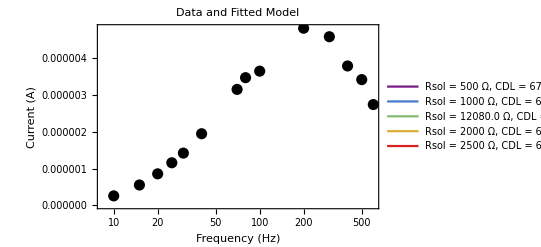

```mathematica
(*STEP 5:Plot fitted curve vs data*)
result2=ReplacePart[result,"Rsol"->500]
result3=ReplacePart[result,"Rsol"->1000]
result4=ReplacePart[result,"Rsol"->2000]
result5=ReplacePart[result,"Rsol"->2500]

fittedModel[f_]:=ModelFunction[f,result];
fittedModel2[f_]:=ModelFunction[f,result2];
fittedModel3[f_]:=ModelFunction[f,result3]
fittedModel4[f_]:=ModelFunction[f,result4]
fittedModel5[f_]:=ModelFunction[f,result5]

rainbowColors=ColorData["Rainbow"]/@Rescale[Range[5]];

legendLabelBestFit=StringTemplate["Rsol = `` Ω, CDL = `` nF (best fit)"][NumberForm[result["Rsol"],{5,1}],NumberForm[result["CDL"]*10^9,{5,0}]];
legendLabelBestFit2=StringTemplate["Rsol = `` Ω, CDL = `` nF"][NumberForm[result2["Rsol"],{5,1}],NumberForm[result2["CDL"]*10^9,{5,0}]];
legendLabelBestFit3=StringTemplate["Rsol = `` Ω, CDL = `` nF"][NumberForm[result3["Rsol"],{5,1}],NumberForm[result3["CDL"]*10^9,{5,0}]];
legendLabelBestFit4=StringTemplate["Rsol = `` Ω, CDL = `` nF"][NumberForm[result4["Rsol"],{5,1}],NumberForm[result4["CDL"]*10^9,{5,0}]];
legendLabelBestFit5=StringTemplate["Rsol = `` Ω, CDL = `` nF"][NumberForm[result5["Rsol"],{5,1}],NumberForm[result5["CDL"]*10^9,{5,0}]];

(*Put your other labels*)
legendLabels={legendLabelBestFit2, legendLabelBestFit3, legendLabelBestFit, legendLabelBestFit4, legendLabelBestFit5};

Show[ListLogLinearPlot[dataBaseline,PlotStyle->{Black,PointSize[0.02]},Frame->True,FrameLabel->{"Frequency (Hz)","Current (A)"},PlotLabel->"Data and Fitted Model"],LogLinearPlot[{fittedModel2[f],fittedModel3[f],fittedModel[f],fittedModel4[f],fittedModel5[f]},{f,1,1000},PlotStyle->(Directive[#,Thick]&/@rainbowColors),PlotRange->All,Frame->True,FrameLabel->{"Frequency (Hz)","Current (A)"},PlotLegends->legendLabels,ImageSize->Large]
]
```

```mathematica
Show[LogLinearPlot[{fittedModel2[f],fittedModel3[f],fittedModel[f],fittedModel4[f],fittedModel5[f]},{f,1,1000},PlotStyle->(Directive[#,Thick]&/@rainbowColors),PlotRange->Automatic,Frame->True,FrameLabel->{"Frequency (Hz)","Current (A)"},PlotLegends->legendLabels,ImageSize->Large]
]
```

-Graphics-